# Optimize Interaction Energy of receptors

Starting from a physical model of channel activation:

```mathematica
(*Energies are in kBT units.*)
Ko[dEo_]:=Exp[-dEo];
Kc[dEc_]:=Exp[-dEc];

(*The Activity Function y(c,params)*)
MWC[c_,dEo_,dEc_,eps_]:=(1+c/Ko[dEo])^5/((1+c/Ko[dEo])^5+Exp[eps]*(1+c/Kc[dEc])^5);
```

We are looking for an optimal way that animals may have used to generate receptors. Here, we first propose that each of the receptors that compose the array have equal probability to be activated along the concentration. Thus, the question is to find the probability distribution of dEo, dEc, and eps that leads to a homogeneous activation probability.

```mathematica
(*2. Define the Input Distribution for c*)(*Uniform distribution between cMin and cMax*)
Pc[c_,cMin_,cMax_]:=Piecewise[{{1/(cMax-cMin),cMin<=c<=cMax}},0];

(*3. Compute the Jacobian term for the change of variable c->y*)
(*We need dy/dc to transform the density*)
dydc[c_,dEo_,dEc_,eps_]=D[MWC[c,dEo,dEc,eps],c]
```

```mathematica
solutionForC=Reduce[{a==aFunc[c,dEo,dEc,eps],c>0},c,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{a==aFunc[c,dEo,dEc,eps],c>0},c,ℝ]

```mathematica
(*4. Express the Conditional Density P(y|parameters)*)
(*P(y)=P(c)/ |dy/dc|*)
(*We need c as a function of y.For MWC,inverting y=f(c) analytically is messy.*)
(*Instead,we define the density parametrically or solve numerically later.*)
(*Analytically,we can write the symbolic condition:*)

PyConditional[y_,dEo_,dEc_,eps_,cMin_,cMax_]:=Module[{sol,cSol,jacobian},
(*Solve for c given y.MWC is monotonic in c,so usually 1 solution exists*)
sol=Solve[y==MWC[cSol,dEo,dEc,eps]&&cSol>0,cSol];
If[Length[sol]==0,0,cSol=cSol/. sol[[1]];(*Extract the concentration*)

(*The Change of Variables Formula*)
(*P(y)=P(c)* |dc/dy| =P(c)/ |dy/dc|*)
(Pc[cSol,cMin,cMax]/Abs[dydc[cSol,dEo,dEc,eps]])]];
```

```mathematica
(*5. Define the Total Probability P(y) by integrating over parameters*)
(*Let rhoEo,rhoEc,rhoEps be the unknown distributions you want to find*)

PyTotal[y_,rhoEo_,rhoEc_,rhoEps_]:=
Integrate[
PyConditional[y,eo,ec,ep,10^-6,10^-1]*rhoEo[eo]*rhoEc[ec]*rhoEps[ep],
{eo,-Infinity,Infinity},
{ec,-Infinity,Infinity},
{ep,-Infinity,Infinity}
];
```

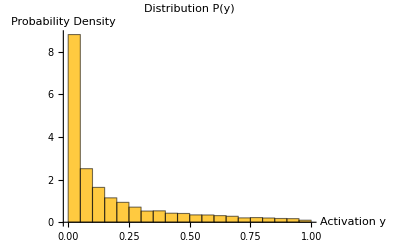

```mathematica
(* ==========================================================*)
(*PRACTICAL IMPLEMENTATION:Numerical check with Gaussian priors*)
(* ==========================================================*)

(*Since the analytical integral above is likely intractable,*)
(*here is how you generate the histogram numerically to check uniformity.*)

Block[{nSamples=10000,cMin=10^-6,cMax=1,samplesY},

(*Draw random parameters from hypothetical distributions*)
(*Example:Eps~Normal[0,2],dEo~Normal[-5,2],dEc~Normal[-2,2]*)
samplesY=Table[
Module[{c,eo,ec,ep,yVal},
c=RandomVariate[UniformDistribution[{cMin,cMax}]];
eo=RandomVariate[NormalDistribution[-5,2]];(*Binding Energy Open*)
ec=RandomVariate[NormalDistribution[-2,2]];(*Binding Energy Closed*)
ep=RandomVariate[NormalDistribution[2,2]];(*Allosteric Energy*)

MWC[c,eo,ec,ep]],{nSamples}];

(*Plot the resulting distribution of y*)
(*If this Histogram is flat,your parameter distributions are optimal.*)
Histogram[samplesY,{0,1,0.05},"PDF",PlotLabel->"Distribution P(y)",AxesLabel->{"Activation y","Probability Density"}]]
```